```mathematica
data={17,18,19,19,20,21,22,23,24,26,27,28,29,30,32,34,35,37,39,42,45,50,58,64,75}
```

{17,18,19,19,20,21,22,23,24,26,27,28,29,30,32,34,35,37,39,42,45,50,58,64,75}

```mathematica
Mean[data]
```

834/25

```mathematica
N[Mean[data]]
```

33.36

```mathematica
StandardDeviation[data]
```

(√(17318/3))/5

```mathematica
N[StandardDeviation[data]]
```

15.1956

```mathematica
EstimatedDistribution[data,NormalDistribution[a,b]]
```

NormalDistribution[33.36,14.8886]

```mathematica
Select[Abs[#-Mean[data]]<=StandardDeviation[data]&][data]
```

{19,19,20,21,22,23,24,26,27,28,29,30,32,34,35,37,39,42,45}

```mathematica
Length[Select[Abs[#-Mean[data]]<=StandardDeviation[data]&][data]]
```

19

```mathematica
Length[Select[Abs[#-Mean[data]]<=StandardDeviation[data]&][data]]/Length[data]
```

19/25

```mathematica
N[Length[Select[Abs[#-Mean[data]]<=StandardDeviation[data]&][data]]/Length[data]]
```

0.76

```mathematica
N[Length[Select[Abs[#-Mean[data]]<=2StandardDeviation[data]&][data]]/Length[data]]
```

0.92

```mathematica
N[Length[Select[Abs[#-Mean[data]]<=3StandardDeviation[data]&][data]]/Length[data]]
```

1.

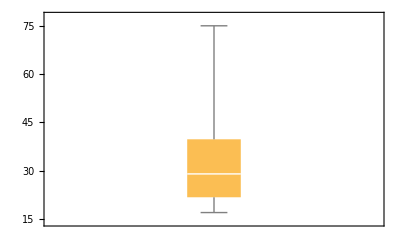

```mathematica
BoxWhiskerChart[data]
```

```mathematica
87/4.
```

21.75

```mathematica
159/4.
```

39.75